# Analysis of Inverted Light Microscope Images

Last updated 06/01/16 by Leanne Friedrich
This notebook is for processing groups of images of printed lines, where particles are dark and the matrix and background are light. 
These images should be sorted into folders, which the ILM interface should do on its own. 
Images should start with ILM and end with .tif

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
<<Functions_ILM.wl;
```

Initialization will give you a variable called directories, which will be a list of sample folders in the directory where you saved this notebook.

```mathematica
Grid[columnIndex[directories][[400;;]]]
```

## Checking for errors

Before running any analysis, you should check to see what your segmented images will look like. To do so, use ILMInterface. This will create an interface where you can input an index of a file in directories, and it will show all ILM images in that folder, and what they look like when the particles are segmented out. If you decide that a file is too bad to repair, use the buttons to delete it. The image will stay showing when you press the button, but you only need to press it once. For analysis, the program will only use the first 7 images.

```mathematica
ILMInterface
```

## Analysis

To analyse images, use getAllImageStats[file, critical intensity for segmenting pixels, critical intensity for segmenting neighboring pixels]
getAllImageStats will just print out the directory name. If you want to identify problems, you must use ILM interface to see what the segmented images look like.

```mathematica
getAllImageStats[directories[[477]], 0.85, 0.3]
```

LF59\SiO7_A16_CSph120\V0\LF59_SiO7_A16_CSph120_V0_P1404_S5_t16_04_08_17_05_07

If you want to know what the composite profile looks like for a sample, use getILMProfile[the name of the directory]

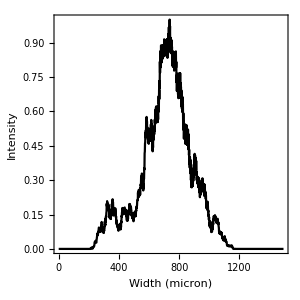
-Graphics-	 | Composite center (Âµm) | Composite STDEV (Âµm)
Image 1 | 747.694 | 198.86
Image 2 | 744.85 | 174.002
Image 3 | 691.99 | 152.19
Image 4 | 731.506 | 144.46
Image 5 | 695.034 | 171.597
Image 6 | 690.593 | 160.477
Image 7 | 678.046 | 147.699
MEAN | 711.388 | 164.183

```mathematica
getILMProfile[directories[[2]]]
```